# ER by DNM with negative DD

## model

lotka-volterra competition

```mathematica
dNadt=Na(ra-Na-β NA); (*wildtype*)
dNAdt=NA(rA-NA-α Na); (*mutant*)
```

like eqn A.3 in Czuppon et al 2023

for simplicity ignore sgv and just think about rescue from dnm, starting with Na=1, NA=0

then the prob of rescue is 1 - Exp[-∫ Na(t) u p_est(t) dt]. We next get Na and p_est then try to integrate.

## wildtype decline

wildtype decline

```mathematica
DSolve[{D[Na[t],t]==(dNadt/.NA->0/.Na->Na[t]), Na[0]==Na0},Na[t],t];
Nat = Na[t]/.Flatten[%]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

(ⅇ^(ra t) Na0 ra)/(-Na0+ⅇ^(ra t) Na0+ra)

this is eqn A.2 in Czuppon et al 2023 with xs=Na, γ=1, β-δ-α=ra

```mathematica
Nat-Na0/(Na0/ra+(1-Na0/ra) ⅇ^(-ra t))//Simplify
```

0

note we decline quicker at first due to competition (density-dependence)

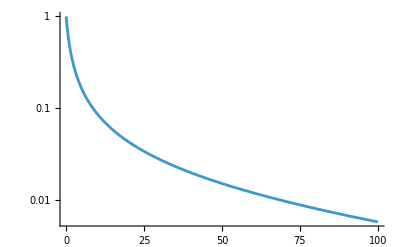

```mathematica
LogPlot[Nat/.{Na0->1, ra->-0.01},{t,0,10^2},PlotRange->All]
```

### establishment probability

The growth rate of the mutant increases with time as competition is relaxed

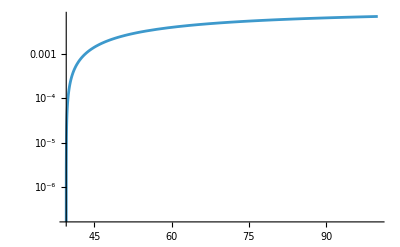

```mathematica
D[dNAdt,NA]/.Na->Nat/.{NA->0,Na0->1, ra->-0.01,rA->0.01,α->0.5};
LogPlot[%,{t,0,10^2},PlotRange->All]
```

To get the establishment probability of a mutant arising at time t we use the expression from Uecker et al 2011 (eqn 16a). This depends on both the mutant growth rate (birth - death) and the sum of mutant birth and death rates. The mutant growth rate is rA - NA - α Na, and we can assume NA=0. If we split this growth between birth and death in some way that the Na term cancels out, eg, bA = 1/2 + rA/2 - α Na/2 and dA =1/2 - rA/2 + α Na/2 (see also Uecker et al 2014 eqn A2), then we can do the double integral:

```mathematica
(*i1=Integrate[D[dNAdt,NA]/.NA->0/.Na->Nat/.t->τ,{τ,T,t}]*)
```

```mathematica
(*i2=Integrate[Exp[-i1],{t,T,∞},Assumptions->{rA>0,α>0,ra<0,Na0>0,T>0}]*)
```

just copying the answer here  to be faster

```mathematica
i2=((-Na0+ra)^α ((-1+ⅇ^(ra T)) Na0+ra)^-α Hypergeometric2F1[-rA/ra,-α,1-rA/ra,(ⅇ^(ra T) Na0)/(Na0-ra)])/rA;
```

the establishment probability is then

```mathematica
pest =2/(1+i2)
```

2/(1+((-Na0+ra)^α ((-1+ⅇ^(ra T)) Na0+ra)^-α Hypergeometric2F1[-rA/ra,-α,1-rA/ra,(ⅇ^(ra T) Na0)/(Na0-ra)])/rA)

check that this reduces to Uecker et al 2011 eqn 17

```mathematica
pest/.α->0//Simplify
```

(2 rA)/(1+rA)

warning: this is not what Czuppon et al 2023 get. They seem to replace mutant growth rate with mutant selective advantage (incorrect), which is a constant when α=β (allowing them to get a solution in a special case).   See their discussion between eqns B.7 and B.8, and their Mathematica notebook: https://github.com/pczuppon/AMRWithinHost/blob/main/SI/Mathematica/withinHost_densityBirth.nb. I haven’t talked with Pete about this yet.

Uecker et al 2011 discuss a rescue scenario in their appendix, but numerically solve for pest and prescue

Uecker et al 2014 only give numerical results for prescue with competition

but can one figure out the dependence of prescue on N0 in all these scenarios without worrying about solving the integrals?

## probability of rescue

to get the probability of rescue from dnm we need to integrate the following over time

```mathematica
rdnm=Nat (pest/.T->t) u
```

(2 ⅇ^(ra t) Na0 ra u)/((-Na0+ⅇ^(ra t) Na0+ra) (1+((-Na0+ra)^α ((-1+ⅇ^(ra t)) Na0+ra)^-α Hypergeometric2F1[-rA/ra,-α,1-rA/ra,(ⅇ^(ra t) Na0)/(Na0-ra)])/rA))

not possible in general but just consider α=1

```mathematica
rdnm1=rdnm/.α->1//Simplify
```

(2 ⅇ^(ra t) Na0 ra (ra-rA) rA u)/(ra (ra-rA) (1+rA)-(-1+ⅇ^(ra t)) Na0 rA (1+rA)+Na0 ra (-1+(-1+ⅇ^(ra t)) rA))

and simplify with r small (and therefore also N0 small, and t large)

```mathematica
rdnm1app=Normal[Series[rdnm1/.ra->ra ϵ/.rA->rA ϵ/.Na0->Na0 ϵ/.t->t/ϵ,{ϵ,0,1}]]/.ϵ->1
```

(2 ⅇ^(ra t) Na0 ra (ra-rA) rA u)/(ra (ra-rA)-Na0 (ra+(-1+ⅇ^(ra t)) rA))

giving

```mathematica
pdnm1=Integrate[rdnm1app,{t,0,∞},Assumptions->{ra<0}]
```

-2 (ra-rA) u (Log[-((Na0-ra) (ra-rA))]-Log[ra (-Na0+ra-rA)])

which can be rearranged into

```mathematica
2 (rA-ra) u Log[((Na0-ra) (rA-ra))/(-ra (Na0+rA-ra))]
```

```mathematica
2 (rA-ra) u (Log[(rA-ra)/-ra]+Log[(Na0-ra)/(Na0+rA-ra)])
```

which shows that there is a very weak relation with initial population size, Na0? Because while it increases the number of mutants that appear it also reduces the probability they establish?

contrast with case where establishment not impacted by wildtype, and rescue increases with log(Na0)

```mathematica
rdnm/.α->0//Simplify
pdnm0=Integrate[%,{t,0,∞},Assumptions->ra<0]
```

(2 ⅇ^(ra t) Na0 ra rA u)/(((-1+ⅇ^(ra t)) Na0+ra) (1+rA))

(2 rA u Log[1-Na0/ra])/(1+rA)

which is still in contrast to the classic case of an exponentially declining wildtype, where rescue depends on Na0

```mathematica
Na0 Exp[ra t]u (pest/.T->t/.α->0)
pclassic=Integrate[%,{t,0,∞},Assumptions->ra<0]
```

(2 ⅇ^(ra t) Na0 u)/(1+1/rA)

-(2 Na0 rA u)/(ra+ra rA)

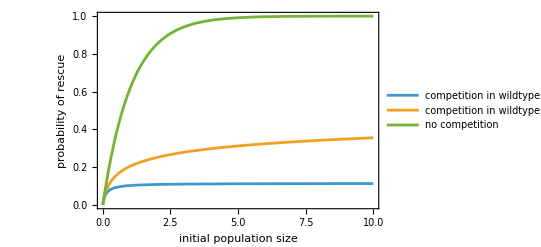

```mathematica
{1-Exp[-p]}/.p->{pdnm1,pdnm0,pclassic}/.ra->-0.1/.u->1/.rA->0.05;
Plot[%,{Na0,0,10},PlotLegends->LineLegend[{"competition in wildtype decline and mutant establishment","competition in wildtype decline only", "no competition"}],Frame->{True,True,False,False},FrameLabel->{"initial population size","probability of rescue"}]
```

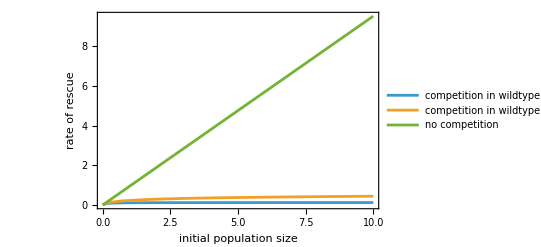

10000

-Graphics-

```mathematica
p/.p->{pdnm1,pdnm0,pclassic}/.ra->-0.1/.u->1/.rA->0.05;
Plot[%,{Na0,0,10},PlotLegends->LineLegend[{"competition in wildtype decline and mutant establishment","competition in wildtype decline only", "no competition"}],Frame->{True,True,False,False},FrameLabel->{"initial population size","rate of rescue"}]
```

```mathematica
Clear[bw,dw,bm,dm,N0,K,mu,t,x,y,rw,rm,Kw,A,J,E1,E2,Prescue];
```

```mathematica
rw=bw-dw;
rm=bm-dm;
Kw=K*(rw/bw);           (*Kw=(1-dw/bw) K*)
A=Kw/N0-1;           (*A=Kw/N0-1*)

(* ====Hypergeometric shorthand====*)
F[p_,q_,x_]:=Hypergeometric2F1[p,q,1+p,x];

(* ====J(x) definition====*)
J[x_]:=(1-x)^(-bm/bw)*(((bm+dm)/rm)*F[-rm/rw,-bm/bw,x]-(bm*x)/(bw*(1-rm/rw))*F[1-rm/rw,1-bm/bw,x]);

(* ====Establishment probability====*)
pest[x_]:=2/(1+J[x]);


pest[0]
pestapprox[x_]:=Normal[FullSimplify[Series[pest[x],{x,0,1}], Assumptions -> { bm>dm >0, dw > bw > 0 }]]
```

2/(1+(bm+dm)/(bm-dm))

```mathematica
integrand[x_] := x pestapprox[x]/(1-x)
```

```mathematica
pres =FullSimplify[ Integrate[integrand[x], {x,0,(N0/K)/(N0/K - rw/bw)},  Assumptions -> { bm>dm >0, dw > bw > 0 , N0>0,K>0}]  ]
```

-(((bm-dm) (bw N0 (2 (bw-dw) (-bm bw+bw^2-bw dw+dm dw) K+bw (bw (2 bm-2 bw+dm)+(2 bw-3 dm) dw) N0)+2 ((bm-bw) bw+(bw-dm) dw) (dw K+bw (-K+N0))^2 Log[((bw-dw) K)/(bw K-dw K-bw N0)]))/(2 bm bw (bm-bw-dm+dw) (dw K+bw (-K+N0))^2))

```mathematica
F[p_,q_,x_]:=Hypergeometric2F1[p,q,1+p,x];
J2[x_]:=(1-x)^(-gm/gw)*(((bm+dm)/rm)*F[-rm/rw,-gm/gw,x]+(gm*x*(2 am - 1))/(gw*(1-rm/rw))*F[1-rm/rw,1-gm/gw,x]);
pest[x_]:=2/(1+J2[x]);
pestapprox[x_]:=Normal[FullSimplify[Series[pest[x],{x,0,1}], Assumptions -> { bm>dm >0, dw > bw > 0 }]]
pestapprox[x]
```

(2 rm)/(bm+dm+rm)+(2 gm rm (bm+dm+(-1+2 am) rm) rw x)/(gw (bm+dm+rm)^2 (rm-rw))